## Study the sampled parameters

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
transPars=Import["unsaturationSamplingVaringK.csv"];
pars=Transpose[transPars];
```

```mathematica
usIndices=Flatten[Position[transPars[[15]],_?(#>0.8&)]];
adIndices=Flatten[Position[transPars[[16]],_?(#>0.3&)]];
usPars=pars[[usIndices]];adPars=pars[[adIndices]];
```

```mathematica
data1=Transpose[{Log10[Transpose[usPars][[18]]],Log10[Transpose[usPars][[19]]]}];
data2=Transpose[{Log10[Transpose[usPars][[20]]],Log10[Transpose[usPars][[21]]]}];
data3=Transpose[{Log10[Transpose[adPars][[18]]],Log10[Transpose[adPars][[19]]]}];
data4=Transpose[{Log10[Transpose[adPars][[20]]],Log10[Transpose[adPars][[21]]]}];
```

```mathematica
plotRange={{-6,6},{-6,6}};
```

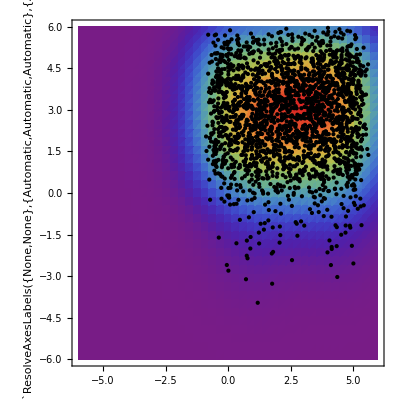

```mathematica
Show[SmoothDensityHistogram[data1,1,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotRange->plotRange],Graphics[Point@data1],PlotRange->plotRange]
```

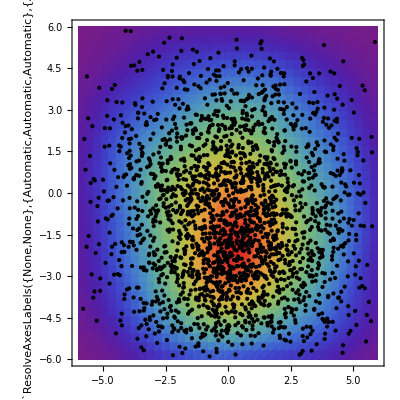

```mathematica
Show[SmoothDensityHistogram[data2,1,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotRange->plotRange],Graphics[Point@data2],PlotRange->plotRange]
```

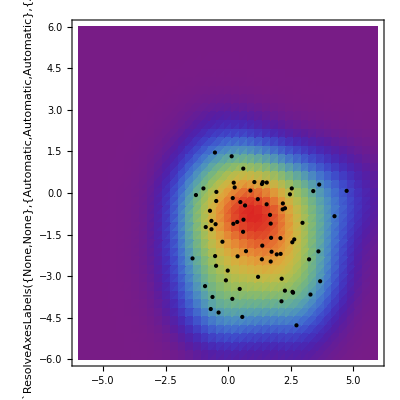

```mathematica
Show[SmoothDensityHistogram[data3,1,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotRange->plotRange],Graphics[Point@data3],PlotRange->plotRange]
```

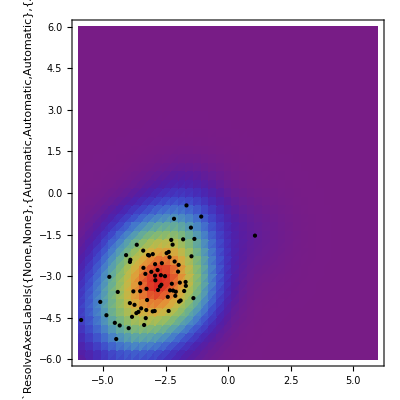

```mathematica
Show[SmoothDensityHistogram[data4,1,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotRange->plotRange],Graphics[Point@data4],PlotRange->plotRange]
```

## Test

```mathematica
Length[adIndices]
```

306

```mathematica
Length[usIndices]
```

3277

```mathematica
heatMap[data_,opts:OptionsPattern[]]:=Module[{n,size,xRange,pr},n="Points"/.{opts}/.{"Points"->100};
pr=PlotRange/.{opts}/.{PlotRange:>Map[{Min[#],Max[#]}&,Transpose[data]]};
xRange=-Subtract@@pr[[1]];
size=Floor[n ("Radius"/.{opts}/.{"Radius"->xRange/6})/xRange];
Graphics[{Inset[ArrayPlot[Rescale@GaussianFilter[ImageData@ColorNegate@ColorConvert[Rasterize[Graphics[Point[data],Background->White,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,PlotRange->pr],"Image",ImageSize->n],"GrayScale"],{3 size,size},Padding->0],ColorFunction->(ColorFunction/.{opts}/.{ColorFunction->ColorData["LakeColors"]}),ImagePadding->0,PlotRangePadding->0,Frame->False],pr[[All,1]],{0,0},xRange]},PlotRange->pr,Frame->True,PlotRangePadding->Scaled[.02]]]
```

```mathematica
data=Transpose[{Log10[Transpose[adPars][[18]]],Log10[Transpose[adPars][[19]]]}];
```

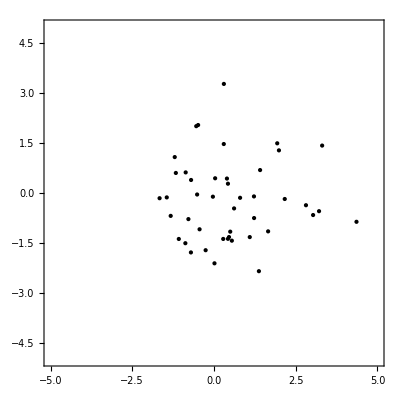
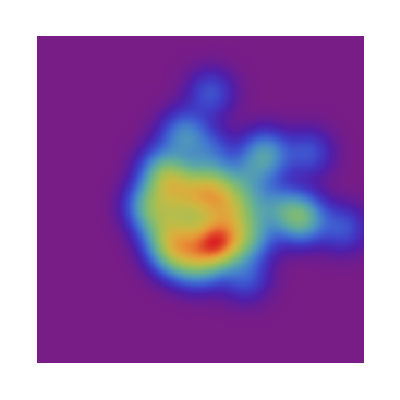

```mathematica
Show[heatMap[data,"Points"->300,"Radius"->.5,PlotRange->{{-5,5},{-5,5}},ColorFunction->ColorData["Rainbow"]],Graphics[Point@data],PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
data=Transpose[{Log10[Transpose[usPars][[18]]],Log10[Transpose[usPars][[19]]]}];
```

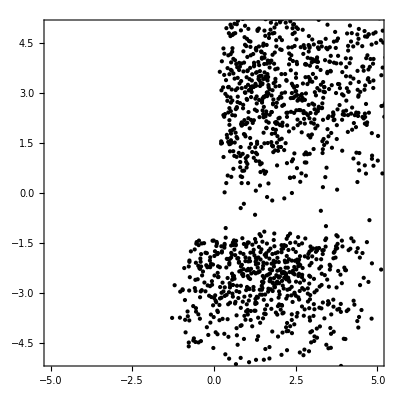
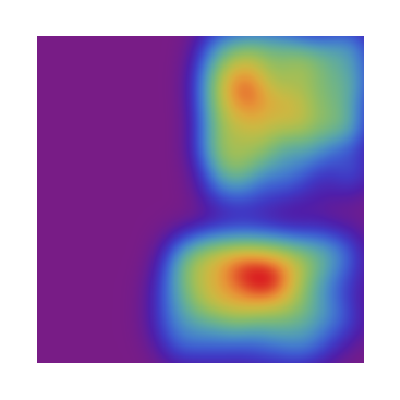

```mathematica
Show[heatMap[data,"Points"->300,"Radius"->.5,PlotRange->{{-5,5},{-5,5}},ColorFunction->ColorData["Rainbow"]],Graphics[Point@data],PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
Show[heatMap[data1,"Points"->300,"Radius"->.5,PlotRange->{{-5,5},{-5,5}},ColorFunction->ColorData["Rainbow"]],Graphics[Point@data1],PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-
-Graphics-